```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ρ1[x_,rx_,ry_,n_]:=ry (1-Abs[x/rx]^n)^(1/n)
ρ2[x_,rx_,ry_,n_]:=-ry (1-Abs[x/rx]^n)^(1/n)
```

```mathematica
Export["LameEllipse.eps",
Plot[{ρ1[x,3,1,0.5],ρ1[x,3,1,1],ρ1[x,3,1,2],ρ1[x,3,1,5],ρ2[x,3,1,0.5],ρ2[x,3,1,1],ρ2[x,3,1,2],ρ2[x,3,1,5]},{x,-3,3},PlotRange->All,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","x_2"},PlotStyle->{Black,{Black,Dashing[0.025]},{Black,DotDashed},{Black,Dashing[0.05]}},PlotLegends->{"n = 0.5", "n = 1", "n = 2", "n = 5"}]
]
```

LameEllipse.eps

```mathematica
ρ[x_,y_,rx_,ry_,n_]:=(Abs[x/rx]^n+Abs[y/ry]^n)^(1/n)
ϕ[x_,y_,p_,q_,rx_,ry_,n_]:=Piecewise[{{(p n)/(4rx ry Beta[1/n,1/n] Beta[2/p,q+1])(1-(Abs[x/rx]^n+Abs[y/ry]^n)^(p/n))^q, Abs[x/rx]^n+Abs[y/ry]^n≤1}, {0, Abs[x/rx]^n+Abs[y/ry]^n>1}}]
```

```mathematica
rect=Line[{{0,0},{10,0},{10,1},{0,1},{0,0}}];
M0=3;
FZ=15;
LeftP=Table[Arrow[{{0,n/M0},{-0.5,n/M0}}],{n,0,M0}];
RightP=Table[Arrow[{{10,n/M0},{10.5,n/M0}}],{n,0,M0}];
σnL=Text[Style["σ̂·n = 1",FZ],{-0.1,1.35}];
σnR=Text[Style["σ̂·n = 1",FZ],{10.1,1.35}];
AB={Line[{{0,0.5},{10,0.5}}],Text[Style["A",FZ],{0.2,0.7}],Text[Style["B",FZ],{9.8,0.7}]};
Export["LongRect.eps",
Graphics[{Thick,Arrowheads[0.02],rect,LeftP,RightP,σnL,σnR,AB},ImageSize->Full]
]
```

test.eps

```mathematica
σ11Uniform=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02/sigma11.csv"]];
σ11Triangle=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_triangle/sigma11.csv"]];
σ11InvTriangle=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_inv_triangle/sigma11.csv"]];
σ11ShortUniform=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_short_uniform/sigma11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
y0=0;
Export["LongRectStress11VarFx200.eps",
Show[
Plot[{σ11Uniform[x,y0],σ11Triangle[x,y0],σ11InvTriangle[x,y0],σ11ShortUniform[x,y0]},{x,0,10},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","(σ̄)_11"},PlotStyle->{Black,{Black,Dashing[0.0125]},{Black,DotDashed},{Black,Dashing[0.05]}},PlotLegends->Placed[{"f_1","f_2","f_3","f_4"},Scaled[{0.7,0.7}]]],
Graphics[{Text[Style["r = 0.2",22],Scaled[{0.35,0.89}]],Text[Style["x_2 = 0",22],Scaled[{0.35,0.77}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.65}]],Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.52}]]}]
]
]
```

LongRectStress11VarFx200.eps

```mathematica
σ11Loc=Interpolation[Import["data/LongRect/LongRect_loc/sigma11.csv"]];
σ11p12r005=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r005/sigma11.csv"]];
σ11p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/sigma11.csv"]];
σ11p12r02=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02/sigma11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Export["LongRectStress11VarR.eps",
Show[
Plot[{σ11Loc[5,y],σ11p12r005[5,y],σ11p12r01[5,y],σ11p12r02[5,y]},{y,0,1},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"r = 0","r = 0.05","r = 0.1","r = 0.2"},Scaled[{0.7,0.5}]]],
Graphics[{Text[Style["x_1 = 5",22],Scaled[{0.35,0.69}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.52}]],Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.35}]]}]
]
]
```

LongRectStress11VarR.eps

```mathematica
σ11Loc=Interpolation[Import["data/LongRect/LongRect_loc/sigma11.csv"]];
σ11p23r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p23_r01/sigma11.csv"]];
σ11p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/sigma11.csv"]];
σ11p13r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p13_r01/sigma11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Export["LongRectStress11VarP.eps",
Show[
Plot[{σ11Loc[5,y],σ11p23r01[5,y],σ11p12r01[5,y],σ11p13r01[5,y]},{y,0,1},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},Scaled[{0.7,0.5}]]],
Graphics[{Text[Style["x_1 = 5",22],Scaled[{0.35,0.69}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.52}]],Text[Style["r = 0.1",22],Scaled[{0.35,0.35}]]}]
]
]
```

LongRectStress11VarP.eps

```mathematica
σ12Loc=Interpolation[Import["data/LongRect/LongRect_loc/sigma12.csv"]];
σ12p23r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p23_r01/sigma12.csv"]];
σ12p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/sigma12.csv"]];
σ12p13r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p13_r01/sigma12.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Export["LongRectSigma12X1.eps",
Show[
Plot[{σ12p23r01[x,0.1],σ12p12r01[x,0.1],σ12p13r01[x,0.1]},{x,0,10},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","(σ̄)_12"},PlotStyle->{{Black,DotDashed},Black,{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},Scaled[{0.7,0.78}]]],
Graphics[{Text[Style["x_2 = 0.1",22],Scaled[{0.35,0.96}]],Text[Style["r = 0.1",22],Scaled[{0.35,0.84}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.72}]],Text[Style["f = f_1",22],Scaled[{0.35,0.6}]]}]
]
]
```

LongRectSigma12X1.eps

```mathematica
Export["LongRectSigma12X2.eps",
Show[
Plot[{σ12Loc[0.1,y],σ12p23r01[0.1,y],σ12p12r01[0.1,y],σ12p13r01[0.1,y]},{y,0,1},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},Scaled[{0.7,0.8}]]],
Graphics[{Text[Style["x_2 = 0.1",22],Scaled[{0.35,0.95}]],Text[Style["r = 0.1",22],Scaled[{0.35,0.8}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.65}]]}]
]
]
```

LongRectSigma12X2.eps

```mathematica
ϵ11Loc=Interpolation[Import["data/LongRect/LongRect_loc/eps11.csv"]];
ϵ11p12r005=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r005/eps11.csv"]];
ϵ11p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/eps11.csv"]];
ϵ11p12r02=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02/eps11.csv"]];
```

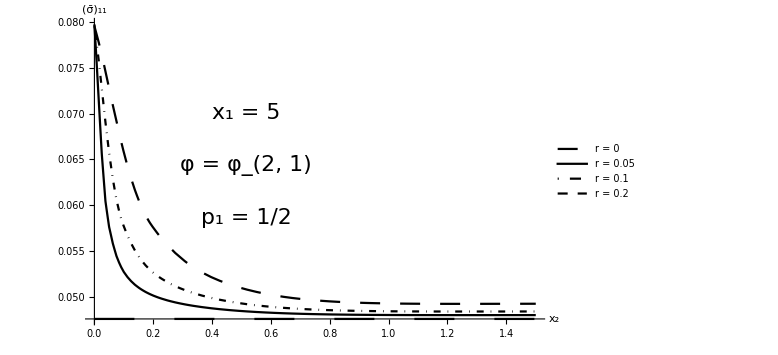

```mathematica
y0=0.;
Show[
Plot[{ϵ11Loc[x,y0],ϵ11p12r005[x,y0],ϵ11p12r01[x,y0],ϵ11p12r02[x,y0]},{x,0,1.5},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"r = 0","r = 0.05","r = 0.1","r = 0.2"},Scaled[{0.7,0.5}]]],
Graphics[{Text[Style["x_1 = 5",22],Scaled[{0.35,0.69}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.52}]],Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.35}]]}]
]
```

```mathematica
ϵ11Loc=Interpolation[Import["data/LongRect/LongRect_loc/eps11.csv"]];
ϵ11p23r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p23_r01/eps11.csv"]];
ϵ11p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/eps11.csv"]];
ϵ11p13r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p13_r01/eps11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

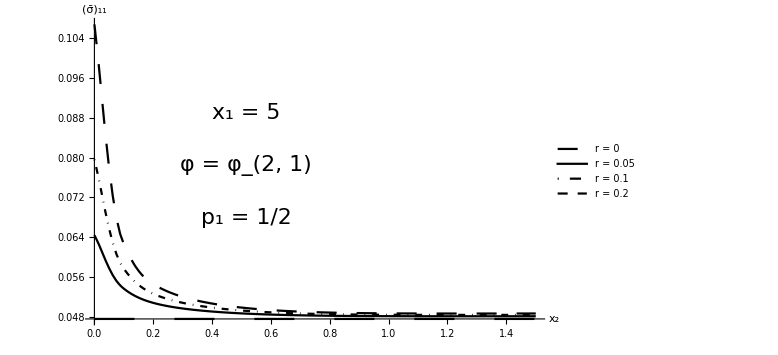

```mathematica
y0=0.;
Show[
Plot[{ϵ11Loc[x,y0],ϵ11p23r01[x,y0],ϵ11p12r01[x,y0],ϵ11p13r01[x,y0]},{x,0,1.5},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"r = 0","r = 0.05","r = 0.1","r = 0.2"},Scaled[{0.7,0.5}]]],
Graphics[{Text[Style["x_1 = 5",22],Scaled[{0.35,0.69}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.52}]],Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.35}]]}]
]
```